```mathematica
(*** in thios program we try  make plot call ternary plot
for this we consider rock paper scissor game
***)
ClearAll[s,p,r,m]
tmax=500;
eq=NDSolve[{r'[t] == s[t]*r[t]-p[t]*r[t],p'[t] ==p[t]*r[t]-s[t]*p[t],s'[t]==s[t]*p[t]-r[t]*s[t],r[0]==0.3,p[0]==0.4,s[0]==0.3},{s,p,r},{t,0,tmax}]
data=Table[Flatten@{r[t]/.eq,p[t]/.eq,s[t]/.eq},{t,0,tmax,0.1}];
Export["a1.txt",data,"TSV"]
```

{{s→InterpolatingFunction[…],p→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

a1.txt

```mathematica
ClearAll[s,p,r,m]
tmax=500;
eq=NDSolve[{r'[t] == s[t]*r[t]-p[t]*r[t],p'[t] ==p[t]*r[t]-s[t]*p[t],s'[t]==s[t]*p[t]-r[t]*s[t],r[0]==0.1,p[0]==0.1,s[0]==0.8},{s,p,r},{t,0,tmax}]
data=Table[Flatten@{r[t]/.eq,p[t]/.eq,s[t]/.eq},{t,0,tmax,0.1}];
Export["a2.txt",data,"TSV"]
```

{{s→InterpolatingFunction[…],p→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

a2.txt

```mathematica
ClearAll[s,p,r,m]
tmax=500;
eq=NDSolve[{r'[t] == s[t]*r[t]-p[t]*r[t],p'[t] ==p[t]*r[t]-s[t]*p[t],s'[t]==s[t]*p[t]-r[t]*s[t],r[0]==0.9,p[0]==0.05,s[0]==0.05},{s,p,r},{t,0,tmax}]
data=Table[Flatten@{r[t]/.eq,p[t]/.eq,s[t]/.eq},{t,0,tmax,0.1}];
Export["a3.txt",data,"TSV"]
```

{{s→InterpolatingFunction[…],p→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

a3.txt

```mathematica
data1=Import["C:\\Users\\Peyman\\Documents\\a1.txt","Table"];
data2=Import["C:\\Users\\Peyman\\Documents\\a2.txt","Table"];
data3=Import["C:\\Users\\Peyman\\Documents\\a3.txt","Table"];
ListPointPlot3D@{data1,data2,data3}
```

-Graphics3D-

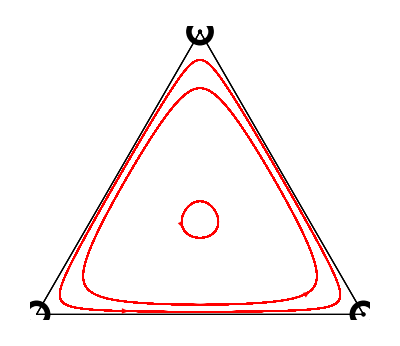

```mathematica
ternaryToCartesian={1/2 (2 #2+#3)/(#1+#2+#3),Sqrt[3]/2 #3/(#1+#2+#3)}&;
background=Graphics[{FaceForm[None],EdgeForm[Directive[Thick,Dashed,Black]],Polygon[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]}];
b11=Graphics[{{PointSize[0.05],Point[{0,0}]},White,PointSize[0.03],Point[{0,0}]}];(*corner point saddle*)
b22=Graphics[{{PointSize[0.05],Point[{1,0}]},White,PointSize[0.03],Point[{1,0}]}];(*corner point saddle*)
b33=Graphics[{{PointSize[0.05],Point[{1/2,Sqrt[3]/2}]},White,PointSize[0.03],Point[{1/2,Sqrt[3]/2}]}];(*corner point saddle*)
b2=Graphics[{{PointSize[Large],Point[{1,0}]},Black,PointSize[Medium],Point[{1,0}]}];(*corner point*)
b3=Graphics[{{PointSize[Large],Point[{1/2,Sqrt[3]/2}]},Black,PointSize[Medium],Point[{1/2,Sqrt[3]/2}]}];(*corner point*)
a11=Show[background,Graphics[{Red,Line[ternaryToCartesian@@@data1]}],AspectRatio->1];
a22=Show[background,Graphics[{Red,Line[ternaryToCartesian@@@data2]}],AspectRatio->1];
a33=Show[background,Graphics[{Red,Line[ternaryToCartesian@@@data3]}],AspectRatio->1];
Show[b11,b22,b33,a11,a22,a33,b2,b3]/.Line->Arrow
```